# Mallinckrodt Functions

## Precipitation

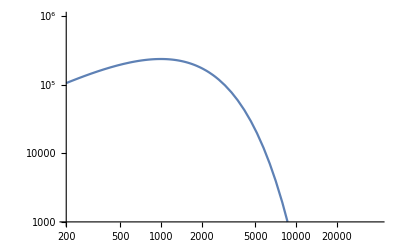

```mathematica
eV2mJ=1.60218 10^-19 10^3(*mJ/eV*);
ϕM[EE_,Q0_,E0_]:=Q0/(2 E0^3)EE Exp[-EE/E0]
LogLogPlot[ϕM[EE,1.3 10^12,1000],{EE,2 10^2,4 10^4},PlotRange->{{2 10^2,4 10^4},{10^3,10^6}}]
```

```mathematica
Q0BG=1.3 10^12 eV2mJ(*mW m^-2*)
E0BG=1000(*eV*)
```

0.000208283

1000

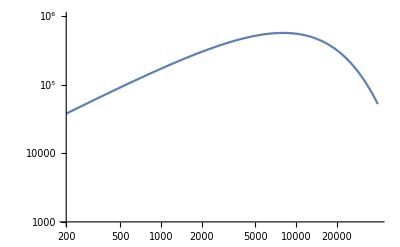

```mathematica
LogLogPlot[ϕM[EE,2 10^14,8000],{EE,2 10^2,4 10^4},PlotRange->{{2 10^2,4 10^4},{10^3,10^6}}]
```

```mathematica
Q0ARC=2 10^14 eV2mJ
E0ARC=8000(*eV*)
```

0.0320436

8000

```mathematica
ee=1.60218 10^-19(*C*);
cc=2.99792 10^8(*m/s*);
me=0.510999 10^6/cc^2(*eV/m^2/s^2*);
eV2mJ=1.60218 10^-19 10^3(*mJ/eV*);
Jacc[nacc_(*m^-3*),E0_(*eV*)]:=ee/Sqrt[2me] nacc Sqrt[E0](*qnv from Kjell Rönnmark (2002)*)
```

## Functions

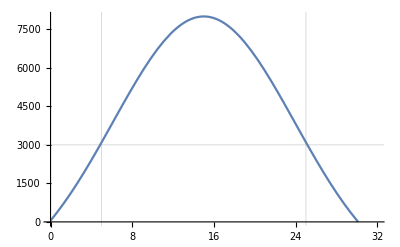

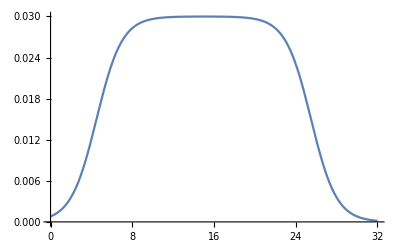

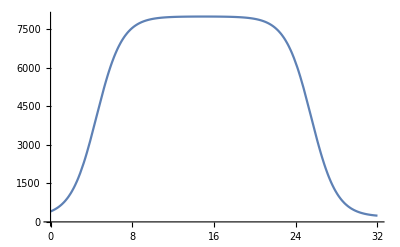

```mathematica
sheet[x_,p_,w_,g_]:=(Tanh[2(x-p+w/2)/g]-Tanh[2(x-p-w/2)/g])/2
V0[X_]:=-2500+(8000+2500)Exp[-4Log[2]((X-15)/21)^2]
Q[X_]:=0.03sheet[X,15,21,5]
E0[X_]:=200+(8000-200)sheet[X,15,21,5]
Plot[V0[X],{X,0,32},PlotRange->{{0,32},{0,8000}},GridLines->{15+20/2{-1,1},{3000}}]
Plot[Q[X],{X,0,32},PlotRange->{{0,32},{0,0.03}},GridLines->{15+21/2{-1,1},{0.03/2}}]
Plot[E0[X],{X,0,32},PlotRange->{{0,32},{0,8000}},GridLines->{15+21/2{-1,1},{8000/2}}]
```

```mathematica
sig=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\aurora_null_01\\conductances\\20150201T100230.000UT_sig.mat"];
```

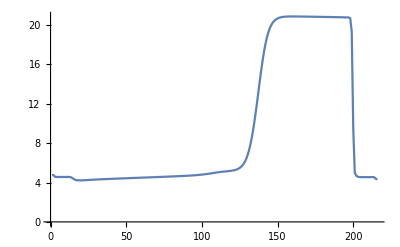

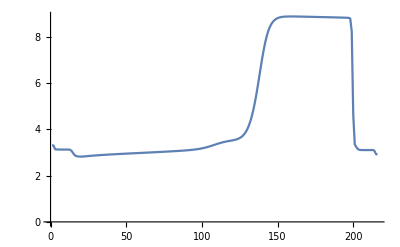

```mathematica
ListLinePlot[-sig[[4,144/2]]]
ListLinePlot[sig[[3,144/2]]]
```